{c→16.8078,k→0.240883,b→18.5537}

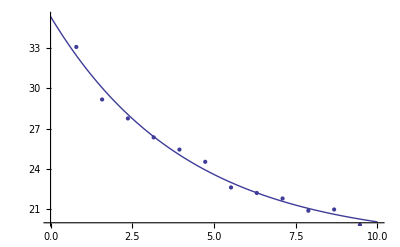

```mathematica
data = {
{0.7886,33.0898728},
{1.5772,29.1797456},
	{2.3658,27.7696184},
	{3.1544,26.3594912},
	{3.943,25.449364},
	{4.7316,24.5392368},
	{5.5202,22.6291096},
	{6.3088,22.2189824},
	{7.0974,21.8088552},
	{7.886,20.898728},
	{8.6746,20.9886008},
	{9.4632,19.8339128093}
};
model = c*Exp[-k*x]+b;
fit = FindFit[data,model,{c,k,b},x,MaxIterations->100000]
ffit = model/. fit;
plot = Plot[ffit, {x,0,10}];
pdata = ListPlot[data];
Show[plot,pdata]
```